```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];
TreeFormToGraph[treeForm_]:=Module[
{graph,tree=ToExpression@ToBoxes@treeForm,order,pos,label},
label=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity];
{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
graph = Graph[DirectedEdge@@@order,VertexLabels->label,VertexCoordinates->MapIndexed[Rule[First[#2],#]&,pos]];
{graph,ReleaseHold[label]}
];
```

```mathematica
FullAdder[a,b,c]
```

{BitOr[BitAnd[a,b],BitAnd[c,BitXor[a,b]]],BitXor[a,b,c]}

```mathematica
{graph,labels} = TreeFormToGraph[TreeForm[FullAdder[a,b,c]]];
```

```mathematica
EdgeList[graph]
```

{1->2,1->11,2->3,2->6,3->4,3->5,6->7,6->8,8->9,8->10,11->12,11->13,11->14}

```mathematica
RuleListToMatrix[list_]:=Transpose[{list[[All,1]],list[[All,2]]}];
```

```mathematica
RuleListToMatrix[ReleaseHold[labels]]
```

{{1,List},{2,BitOr},{3,BitAnd},{4,a},{5,b},{6,BitAnd},{7,c},{8,BitXor},{9,a},{10,b},{11,BitXor},{12,a},{13,b},{14,c}}

```mathematica
SeparateFirst[l_]:={First[l],Drop[l,1]};
```

```mathematica
{fixed,toBeReplaced}=SeparateFirst[Cases[RuleListToMatrix[ReleaseHold[labels]],{vertex_,a}:>vertex]]
```

{4,{9,12}}

```mathematica
MakeReplaceRules[fixed_,toBeReplaced_]:=Map[(vertex_->#):>(vertex->fixed)&,toBeReplaced];
```

```mathematica
MakeReplaceRules[fixed,toBeReplaced]
```

{vertex$_->9:>vertex$->4,vertex$_->12:>vertex$->4}

```mathematica
EdgeList[graph]
```

{1->2,1->11,2->3,2->6,3->4,3->5,6->7,6->8,8->9,8->10,11->12,11->13,11->14}

```mathematica
ReplaceAll[EdgeList[graph],MakeReplaceRules[fixed,toBeReplaced]]
```

{1->2,1->11,2->3,2->6,3->4,3->5,6->7,6->8,8->4,8->10,11->4,11->13,11->14}

```mathematica
ReplaceRuleForLabel[labels_,labelName_]:=Block[{fixed,toBeReplaced,replaceRules},
{fixed,toBeReplaced}=SeparateFirst[Cases[RuleListToMatrix[labels],{vertex_,labelName}:>vertex]];
replaceRules = MakeReplaceRules[fixed,toBeReplaced];
MakeReplaceRules[fixed,toBeReplaced]
];
ReplaceRuleForAllLabels[labels_]:=Block[{nameLabels},
nameLabels = DeleteCases[
DeleteDuplicates[labels[[All,2]]],
x_ /;MemberQ[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association},x]
];
Flatten[Map[ReplaceRuleForLabel[labels,#]&,nameLabels]]
];
```

```mathematica
ReplaceRuleForAllLabels[labels]
```

{vertex$_->9:>vertex$->4,vertex$_->12:>vertex$->4,vertex$_->10:>vertex$->5,vertex$_->13:>vertex$->5,vertex$_->14:>vertex$->7}

```mathematica
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]]
```

{1->2,1->11,2->3,2->6,3->4,3->5,6->7,6->8,8->4,8->5,11->4,11->5,11->7}

```mathematica
labels
```

{1→List,2→BitOr,3→BitAnd,4→a,5→b,6→BitAnd,7→c,8→BitXor,9→a,10→b,11→BitXor,12→a,13→b,14→c}

```mathematica
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]]
```

{9,10,12,13,14}

```mathematica
labels
```

{1→List,2→BitOr,3→BitAnd,4→a,5→b,6→BitAnd,7→c,8→BitXor,9→a,10→b,11→BitXor,12→a,13→b,14→c}

```mathematica
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]]
```

{1→List,2→BitOr,3→BitAnd,4→a,5→b,6→BitAnd,7→c,8→BitXor,11→BitXor}

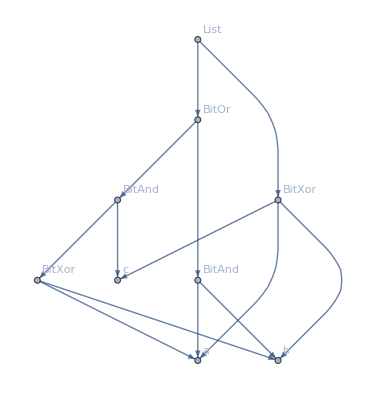

```mathematica
Graph[newGraph,VertexLabels->newLabels,DirectedEdges->True]
```

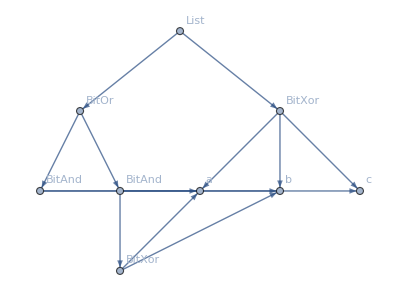

```mathematica
TreePlot[newGraph,VertexLabels->newLabels,DirectedEdges->True]
```

## Forma final

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];
TreeFormToGraph[treeForm_]:=Module[
{graph,tree=ToExpression@ToBoxes@treeForm,order,pos,label},
label=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity];
{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
graph = Graph[DirectedEdge@@@order,VertexLabels->label,VertexCoordinates->MapIndexed[Rule[First[#2],#]&,pos]];
{graph,ReleaseHold[label]}
];

RuleListToMatrix[list_]:=Transpose[{list[[All,1]],list[[All,2]]}];
SeparateFirst[l_]:={First[l],Drop[l,1]};
MakeReplaceRules[fixed_,toBeReplaced_]:=Map[(vertex_->#):>(vertex->fixed)&,toBeReplaced];

ReplaceRuleForLabel[labels_,labelName_]:=Block[{fixed,toBeReplaced,replaceRules},
{fixed,toBeReplaced}=SeparateFirst[Cases[RuleListToMatrix[labels],{vertex_,labelName}:>vertex]];
replaceRules = MakeReplaceRules[fixed,toBeReplaced];
MakeReplaceRules[fixed,toBeReplaced]
];
ReplaceRuleForAllLabels[labels_]:=Block[{nameLabels},
nameLabels = DeleteCases[
DeleteDuplicates[labels[[All,2]]],
x_ /;MemberQ[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association},x]
];
Flatten[Map[ReplaceRuleForLabel[labels,#]&,nameLabels]]
];

CompactTreeForm[expr_]:=Block[{graph,labels,newGraph,deleteVertex,newLabels},
{graph,labels} = TreeFormToGraph[TreeForm[expr]];
newGraph = ReplaceAll[EdgeList[graph],ReplaceRuleForAllLabels[labels]];
deleteVertex = Complement[labels[[All,1]],VertexList[newGraph]];
newLabels = DeleteCases[labels,x_/;MemberQ[deleteVertex,First[x]]];

TreePlot[newGraph,VertexLabels->newLabels,DirectedEdges->True]
];
```

```mathematica
CompactTreeForm[FullAdder[a,b,c]]
```

-Graphics-

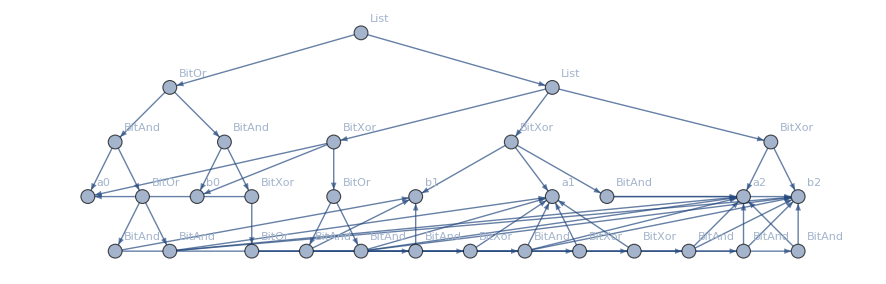

```mathematica
CompactTreeForm[ALUAdder[{a0,a1,a2},{b0,b1,b2}]]
```